## General Principles

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

Exact input ⟹ exact output.

Approximate input ⟹ approximate output.

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

## Free-form Input

In Version 8, there is integration of Wolfram|Alpha. This means that you can use free-form linguistics. The output shows you the Mathematica syntax required to do the same computation.

-Graphics- (== at beginning of input) — use free-form linguistics to generate Mathematica output

(== == at beginning of input) — generate full Wolfram|Alpha output

-Graphics- (Ctrl+==) — enter free-form linguistics for conversion to inline Mathematica input

The following questions require you to use free-form linguistics.

Compute π to 1000 digits. [1 Mark]

WolframAlphaQueryParseResults

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

Integrate sin(x^2) from 0 to ∞. [1 Mark]

WolframAlphaQueryParseResults

(√(π/2))/2

Sum 1/n^2 with n from 1 to ∞. What is the exact value of this sum? [2 Marks]

WolframAlphaQueryResults

1.64493

```mathematica
∑_(n=1)^∞ 1/n^2
```

π^2/6

Solve the simultaneous equations x^2+y^2==1 and x-y==1.  [1 Mark]

WolframAlphaQueryResults

(x==0∨x==1)∧y==x-1

Produce a contour plot of ⅇ^(-x^2-y^2)sin(x+y) over [-1,1]×[-1,1].  [1 Mark]

WolframAlphaQueryResults

-Graphics3D-

Compute a random 10×10 matrix. [1 Mark]

WolframAlphaQueryResults

(0.690864 | 0.648775 | 0.24052 | 0.111853 | 0.32876 | 0.0793739 | 0.276733 | 0.0107537 | 0.863763 | 0.465922
0.194702 | 0.330275 | 0.711963 | 0.048933 | 0.620993 | 0.294574 | 0.936689 | 0.0240498 | 0.106287 | 0.110192
0.282256 | 0.478514 | 0.865635 | 0.963321 | 0.734991 | 0.011674 | 0.25876 | 0.457974 | 0.778721 | 0.132651
0.372332 | 0.0290879 | 0.409902 | 0.441857 | 0.491286 | 0.953506 | 0.0506037 | 0.587224 | 0.396939 | 0.182753
0.172864 | 0.279998 | 0.844319 | 0.487753 | 0.112325 | 0.127338 | 0.322102 | 0.487374 | 0.366705 | 0.669642
0.103305 | 0.489451 | 0.192984 | 0.361041 | 0.687479 | 0.879299 | 0.166681 | 0.0100964 | 0.53184 | 0.524541
0.922654 | 0.52733 | 0.0729165 | 0.467166 | 0.540467 | 0.315666 | 0.232535 | 0.105879 | 0.258095 | 0.356955
0.156356 | 0.307681 | 0.6468 | 0.0357557 | 0.48196 | 0.593835 | 0.472656 | 0.134049 | 0.70733 | 0.89587
0.75719 | 0.661458 | 0.147903 | 0.549813 | 0.790721 | 0.305289 | 0.704266 | 0.521628 | 0.253539 | 0.918632
0.443178 | 0.62015 | 0.972902 | 0.253033 | 0.866567 | 0.311107 | 0.667899 | 0.00804849 | 0.0594117 | 0.392125)

Compute the CO_2 production per capita for Australia. [1 Mark]

WolframAlphaQueryResults

384.2 million tCO_2 e/year (metric tons of carbon dioxide equivalent per year)

## Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively you can use Palettes such as the Basic Math Assistant.

## Numbers

### Integers and rational operations

Integer and rational operations are exact. And you can work with numbers of arbitrary size.

Calculate the exact value of 3 to the 1000^th power. [1 Mark]

```mathematica
3^1000
```

1322070819480806636890455259752144365965422032752148167664920368226828597346704899540778313850608061963909777696872582355950954582100618911865342725257953674027620225198320803878014774228964841274390400117588618041128947815623094438061566173054086674490506178125480344405547054397038895817465368254916136220830268563778582290228416398307887896918556404084898937609373242171846359938695516765018940588109060426089671438864102814350385648747165832010614366132173102768902855220001

### Numerical Evaluation

To obtain numerical values, use N.

Calculate the numerical value of 3 to the 1000^th power. [1 Mark]

```mathematica
N[%]
```

1.32207081948081×10^477

Calculate the numerical value of π. [1 Mark]

```mathematica
N[Pi]
```

3.14159

Calculate the first 1000 digits of π. [1 Mark]

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

Calculate 30 digits of ⅇ^(√163 π). What is the closest integer to ⅇ^(√163 π)? [2 Marks]

```mathematica
N[ⅇ^(√163 π),30]
```

2.62537412640768743999999999999×10^17

```mathematica
Round[%]
```

262537412640768744

### StandardForm and TraditionalForm

To change a cell between standard and traditional from select the cell bracket (on the right) and use  Cell ▶ Convert To ▶ ⋯Form  (or the shortcuts)

To toggle an expression between standard and traditional form select the expression and press Ctrl[N] / Ctrl[T].

Compute Cos[Pi] and cos(π). [2 Marks]

```mathematica
Cos[Pi]
```

-1

```mathematica
cos(π)
```

-1

Note that exact input ⟹ exact output.

Compute Log[10,0.01] and log_2(16). [3 Marks]

```mathematica
Log[10,0.01]
```

-2.

```mathematica
Subscript[log, 2](16)
```

4

### Complex Numbers

Obtain the real (Re) and imaginary (Im) parts of (1+2ⅈ)/(3+4ⅈ) where ⅈ==ⅉ==√-1. [2 Marks]

```mathematica
Re[(1+2 ⅈ)/(3+4 ⅈ)]
```

11/25

```mathematica
Im[(1+2 ⅈ)/(3+4 ⅈ)]
```

2/25

Compute Exp[Log[3]] and exp(log(3)+ⅈ π). [1 Mark]

```mathematica
Exp[Log[3]]
```

3

```mathematica
exp(log(3)+ⅈ π)
```

-3

Apply ComplexExpand (which obtains the real and imaginary parts of an expression) to ⅈ^ⅈ. Is the result real? [2 Marks]

```mathematica
ComplexExpand[ⅈ^ⅈ]
```

ⅇ^(-π/2)

```mathematica
N[%]
```

0.20788

Answer: Yes, the answer is real.

## Symbols

### Algebra

Expand (x^3-3 x^2 y+3x y^2-y^3)^20 and then factor the result. [1 Mark]

```mathematica
(x^3-3 x^2 y+3x y^2-y^3)^20//Expand
```

x^60-60 x^59 y+1770 x^58 y^2-34220 x^57 y^3+487635 x^56 y^4-5461512 x^55 y^5+50063860 x^54 y^6-386206920 x^53 y^7+2558620845 x^52 y^8-14783142660 x^51 y^9+75394027566 x^50 y^10-342700125300 x^49 y^11+1399358844975 x^48 y^12-5166863427600 x^47 y^13+17345898649800 x^46 y^14-53194089192720 x^45 y^15+149608375854525 x^44 y^16-387221678682300 x^43 y^17+925029565741050 x^42 y^18-2044802197953900 x^41 y^19+4191844505805495 x^40 y^20-7984465725343800 x^39 y^21+14154280149473100 x^38 y^22-23385332420868600 x^37 y^23+36052387482172425 x^36 y^24-51915437974328292 x^35 y^25+69886166503903470 x^34 y^26-88004802264174740 x^33 y^27+103719945525634515 x^32 y^28-114449595062769120 x^31 y^29+118264581564861424 x^30 y^30-114449595062769120 x^29 y^31+103719945525634515 x^28 y^32-88004802264174740 x^27 y^33+69886166503903470 x^26 y^34-51915437974328292 x^25 y^35+36052387482172425 x^24 y^36-23385332420868600 x^23 y^37+14154280149473100 x^22 y^38-7984465725343800 x^21 y^39+4191844505805495 x^20 y^40-2044802197953900 x^19 y^41+925029565741050 x^18 y^42-387221678682300 x^17 y^43+149608375854525 x^16 y^44-53194089192720 x^15 y^45+17345898649800 x^14 y^46-5166863427600 x^13 y^47+1399358844975 x^12 y^48-342700125300 x^11 y^49+75394027566 x^10 y^50-14783142660 x^9 y^51+2558620845 x^8 y^52-386206920 x^7 y^53+50063860 x^6 y^54-5461512 x^5 y^55+487635 x^4 y^56-34220 x^3 y^57+1770 x^2 y^58-60 x y^59+y^60

```mathematica
Factor[%]
```

(x-y)^60

### Equations

Compute and simplify both the sum and product of the two roots of the quadratic equation x^2+b x+c==0. 
Explain the resulting simple expressions. [3 Marks]

```mathematica
Solve[x^2+b x+c==0,x]
```

{{x→1/2 (-√(b^2-4 c)-b)},{x→1/2 (√(b^2-4 c)-b)}}

```mathematica
x/.%
```

{1/2 (-√(b^2-4 c)-b),1/2 (√(b^2-4 c)-b)}

```mathematica
Total[%]//Simplify
```

-b

```mathematica
Times@@%%//Simplify
```

c

Written answer: The sum of the two roots is ... because ...

Note that equations involve == or == (a “long” equal siqn). See Equal.

### Indefinite integration

Compute ∫1/(1-x^3)ⅆx and check the result. [3 Marks]

```mathematica
∫1/(1-x^3)ⅆx
```

1/6 log(x^2+x+1)-1/3 log(1-x)+(tan^-1((2 x+1)/(√3)))/(√3)

```mathematica
∂_x %//Simplify
```

1/(1-x^3)

Compute ∫1/(1-x^4)ⅆx using partial fractions and verify the answer. [3 Marks]

```mathematica
Apart[1/(1-x^4)]
```

1/(2 (x^2+1))+1/(4 (x+1))-1/(4 (x-1))

```mathematica
∫1/(2 (x^2+1))ⅆx
```

1/2 tan^-1(x)

```mathematica
∫1/(4 (x+1))ⅆx
```

1/4 log(4 x+4)

```mathematica
∫1/(4 (x-1))ⅆx
```

1/4 log(x-1)

```mathematica
%%%+%%-%
```

-1/4 log(x-1)+1/4 log(4 x+4)+1/2 tan^-1(x)

```mathematica
∂_x %//Simplify
```

1/(1-x^4)

ie. Do this 'semimanually'  using Apart and Integrate.  Then compare with the normal Mathematica result.

Compute ∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx and ∫_0^∞ ⅇ^(-a x)cos(λ x)ⅆx with a>0 and λ∈ℝ. [2 Marks]

```mathematica
Assuming[a>0,∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx]
```

(√π)/(√a)

```mathematica
Assuming[a>0∧λ∈ℝ,∫_0^∞ ⅇ^(-a x)cos(λ x)ⅆx]
```

a/(a^2+λ^2)

### Differential equations

Show that the indefinite integral y(x)==∫_a^x f(t)ⅆt is equivalent to the differential equation y'(x)==f(x) with the initial condition y(a)==0. [2 Marks]

```mathematica
ℰ=y(x)==∫_a^x f(t)ⅆt
```

y(x)==∫_a^x f(t)ⅆt

```mathematica
{(∂ℰ)/(∂x),ℰ/.x->a}
```

{y'(x)==f(x),y(a)==0}

Hint:  This is not a question where you just blindly apply a Mathematica command. Think about what's being asked.

## Graphics

Plot the function x↦x^2/10-(cos(x))^2. Choose a range of x that includes all values of x for which this function is zero. [2 Marks] Use FindRoot to confirm the locations of the above zeros. [2 Marks] Plot the derivative. [1 Mark] Put the above two plots on the same graph. (Hint: look at help file for Plot or alternatively Show) [1 Mark]

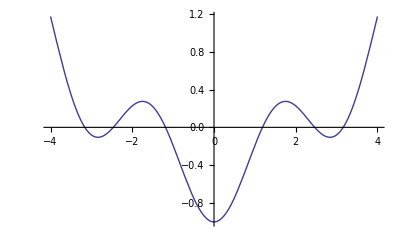

```mathematica
fn=Plot[x^2/10-(cos(x))^2,{x,-4,4}]
```

```mathematica
Table[FindRoot[x^2/10-(cos(x))^2,{x,x0}],{x0,{-3,-2,-1,1,2,3}}]
```

{{x→-3.16164},{x→-2.46433},{x→-1.18626},{x→1.18626},{x→2.46433},{x→3.16164}}

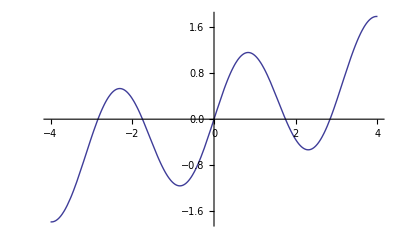

```mathematica
der=Plot[Evaluate[D[(x^2/10-(cos(x))^2), x]],{x,-4,4}]
```

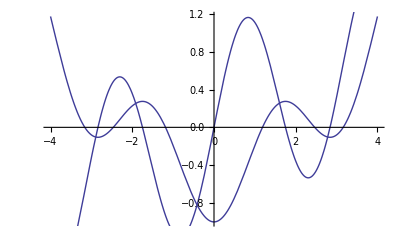

```mathematica
Show[fn,der]
```

Note the use of FindRoot as opposed to Solve.  This is because the equation is transcendental (try using Solve and see what happens).

Use Plot3D to visualize the function {x,y}↦x^2-x y+y^2 over [-1,1]×[-1,1]. [1 Mark]

```mathematica
Plot3D[x^2-x y+y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Use ContourPlot to visualize the function {x,y}↦x^2-x y+y^2 over [-1,1]×[-1,1]. [1 Mark]

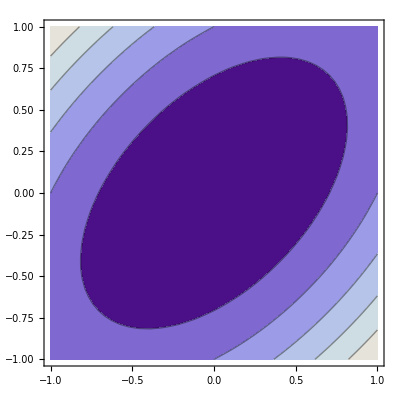

```mathematica
ContourPlot[x^2-x y+y^2,{x,-1,1},{y,-1,1}]
```

Use Plot3D to visualize the function {x,y}↦x^2-x y+y^2 for x^2+y^2≤1. [2 Marks]

```mathematica
Plot3D[x^2-x y+y^2,{x,-1,1},{y,-1,1},RegionFunction->({x,y}↦x^2+y^2≤1)]
```

-Graphics3D-

## Packages

Additional packages can be loaded. For example, after loading the PhysicalConstants` package.

```mathematica
<<PhysicalConstants`
```

one has access to physical constants such as c, e, ℏ, and ϵ_0, along with their SI units.

```mathematica
N[c]=SpeedOfLight
```

```mathematica
N[e]=ElectronCharge
```

```mathematica
N[ℏ]=PlanckConstantReduced
```

```mathematica
N[Subscript[ϵ, 0]]=VacuumPermittivity
```

```mathematica
N[Subscript[m, e]]=ElectronMass
```

ℏ is entered as hb .  ϵ_0 is entered as eCtrl[_]0 .

Instead of assigning the symbols c, e, ℏ, and ϵ_0, we assign their numerical value. In this way we can work with expressions involving these symbols but, if we numerically evaluate such an expression, a numerical value results.

After entering the above inputs, use E=m c^2 to compute the rest-mass energy of an electron in electron volts. You will need to numerically evaluate the energy first and use Convert to obtain energies in electron volts. [2 Marks]

```mathematica
Convert[N[Subscript[m, e] c^2],ElectronVolt]
```

510999. ElectronVolt

The fine structure constant, α, is a dimensionless number that appears in quantum electrodynamics. It is not currently known if it can be derived from first principles in terms of mathematical constants. In SI units (see http://physics.nist.gov/cuu/Units/units.html), α=1/(4π ϵ_0)e^2/(ℏ c). Compute the numerical value of α and show that it is a dimensionless constant (Hint: express the derived units Volt, Coulomb, and Joule in terms of m, Kg, s, and A). Also compute 1/α. [3 Marks]

```mathematica
N[1/(4π Subscript[ϵ, 0])e^2/(ℏ c)]
```

(0.00729735 Coulomb^2 Volt)/(Ampere Joule Second)

```mathematica
%/.{Coulomb->Ampere Second,Joule->(Meter^2 Kilogram)/Second^2,Volt->(Meter^2 Kilogram)/(Second^3 Ampere)}
```

0.00729735

```mathematica
1/%
```

137.036

## Using the Web

At mathworld.wolfram.com/PiFormulas.html you will find a number of formulas for π. Confirm equations (5), (6), and (9). [3 Marks]

```mathematica
π/4==4 tan^-1(1/5)-tan^-1(1/239)
```

True

```mathematica
π/4==∑_(k=1)^∞ (-1)^(k+1)/(2 k-1)
```

True

```mathematica
π==∑_(k=0)^∞ (2(-1)^k 3^(1/2-k))/(2 k+1)
```

True

Lookup the primary definition for log(z) at http://functions.wolfram.com/. Enter this definition into Mathematica and check it. [1 Mark]

```mathematica
log(z)==∑_(k=1)^∞ ((-1)^(k-1) (z-1)^k)/k
```

True